url: http://bit.ly/2eajQDL

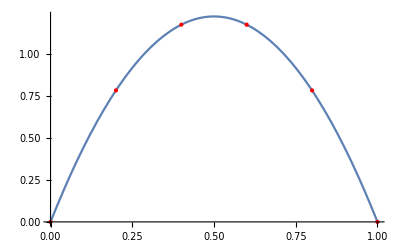

```mathematica
pts=RandomReal[{-1,1},{4}];
(*;*)
pts={.25,.25,.25,.25};
pts={0.784,1.176,1.1760000000000002,0.7839999999999994};
coords=Join[{{0,0}},Table[{i/(Length[pts]+1),pts[[i]]},{i,Length[pts]}],{{1,0}}];
int=Interpolation[coords,Method->"Spline",InterpolationOrder->3];
integral=NIntegrate[1/2 int'[t]^2-9.8 int[t],{t,0,1}];
frames=Table[Graphics[{PointSize[0.05],Red,Point[{0,int[t]}],Blue,InfiniteLine[{0,0},{1,0}],Black,Text[integral,{-0.5,0.5}]},PlotRange->1.5],{t,0,1,.02}];
Plot[int[t],{t,0,1},Epilog->{PointSize->0.05,Red,Point/@coords}]
ListAnimate[frames]
```

```mathematica
1/2 9.8 0.5^2
```

1.225

```mathematica
9.8 0.5
```

4.9

```mathematica
Table[4.9 t-1/2 9.8 t^2,{t,0.2,1-0.2,0.2}]
```

{0.784,1.176,1.176,0.784}

```mathematica
Integrate[1/2(4.9-9.8 t)^2-9.8(4.9t-1/2 9.8 t^2),{t,0,1}]
```

-4.00167